# Social Network Analysis

## Chen Avin School of Electrical and Computer Engineering

# Unit 9 Scale Free Graphs and Power Laws Degree Distributions

(Based on Networks: An Introduction. By M.E.J Newman, and Slides by Lada Adamic)

## Last Time

Random Graphs models

Erdös-Rényi Graph model

Simple model

Giant Component

Short Path length

Poisson / Binomial Degree Distribution

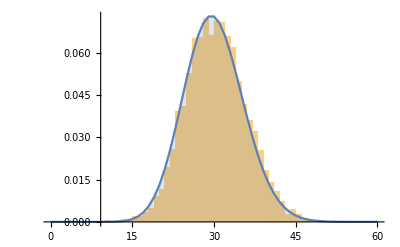

## What happens in real life?

Network of Thrones

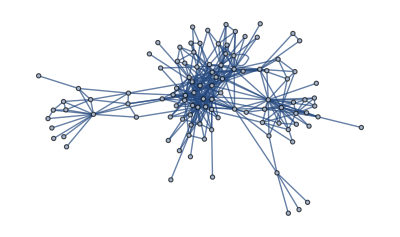

```mathematica
SetDirectory[NotebookDirectory[]];
file = Rest[Import["data/stormofswords.csv"]];
tribes = Import["data/tribes.csv"];
nodes =Flatten[tribes[[All,1]]];
edges =#[[1]]<->#[[2]]&/@ file [[All,{1,2}]];
ThronesG =Graph[nodes,edges, VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
maxDegree = Max[VertexDegree[ThronesG]];
avgDegree = Mean[VertexDegree[ThronesG]]//N;
minDegree = Min[VertexDegree[ThronesG]];
size = VertexCount[ThronesG];
```

Network Size

```mathematica
size
```

107

Max Degree, Avrg. Degree, Min Digree

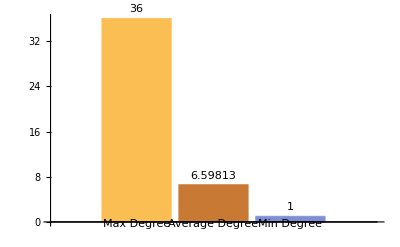

```mathematica
BarChart[{{maxDegree,avgDegree,minDegree}},ChartLabels->{"Max Degree","Average Degree","Min Degree"}, LabelingFunction->Above]
```

Let’s try to fit Binomial Distribution

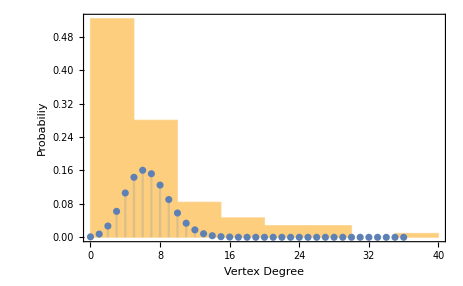

```mathematica
Show[Histogram[VertexDegree[ThronesG],Automatic,"Probability",PlotRange->All,FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True],DiscretePlot[Evaluate@PDF[BinomialDistribution[size,avgDegree/size],k],{k,0,maxDegree,1}, PlotRange->{0,maxDegree,5},FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True]]
```

Let’s try to fit Exponential Distribution (looks good)

```mathematica
PDF[ExponentialDistribution[λ],x]
```

Piecewise[{{ⅇ^(-x λ) λ, x≥0}, {0, True}}]

```mathematica
Mean[ExponentialDistribution[λ]]
```

1/λ

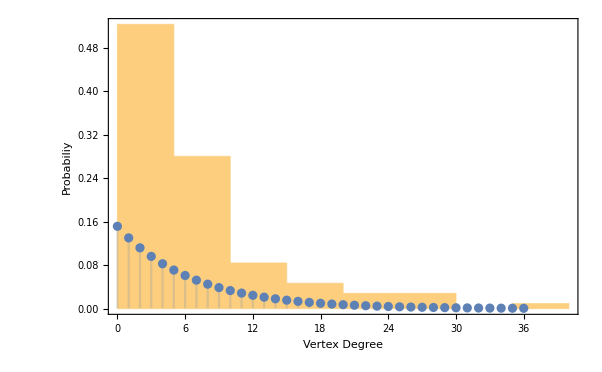

```mathematica
Show[Histogram[VertexDegree[ThronesG],Automatic,"Probability",PlotRange->All,FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True],DiscretePlot[Evaluate@PDF[ExponentialDistribution[1/avgDegree],k],{k,0,maxDegree,1}, PlotRange->All,FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True]]
```

## Class Facebook Network

```mathematica
SetDirectory["/Users/avin/Dropbox/SocialNetworkClass/FacebookStudents/MyTry"];
fbNodes = Import["ClassVertexList.csv",CharacterEncoding-> "UTF8"];
fbEdges = Import["ClassEdgeList.csv" ,CharacterEncoding-> "UTF8"];
class= Import["students.csv" ,CharacterEncoding-> "UTF8"];
ClassFBall =Graph[Flatten[fbNodes],#[[1]]<->#[[2]] &/@ fbEdges,VertexLabels->Placed["Name",Tooltip]];
maxDegree = Max[VertexDegree[ClassFBall]];
avgDegree = Mean[VertexDegree[ClassFBall]]//N;
minDegree = Min[VertexDegree[ClassFBall]];
size = VertexCount[ClassFBall];
```

Network Size

```mathematica
size
```

10095

Max Degree, Avrg. Degree, Min Digree

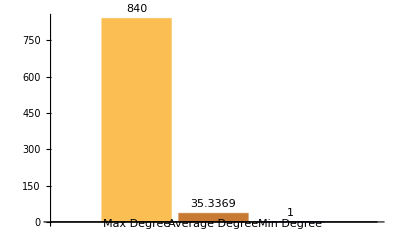

```mathematica
BarChart[{{maxDegree,avgDegree,minDegree}},ChartLabels->{"Max Degree","Average Degree","Min Degree"}, LabelingFunction->Above]
```

Let’s try to fit Binomial Distribution

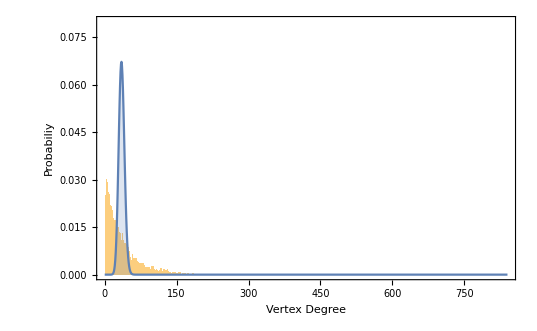

```mathematica
Show[Histogram[VertexDegree[ClassFBall],{0,maxDegree,1},"Probability",PlotRange->{{0,maxDegree},{0,0.08}},FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True],DiscretePlot[Evaluate@PDF[BinomialDistribution[size,avgDegree/size],k],{k,0,maxDegree,1}, PlotRange->{{0,maxDegree},{0,0.08}},FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True]]
```

Let’s try to fit Exponential Distribution (looks good)

```mathematica
PDF[ExponentialDistribution[λ],x]
```

Piecewise[{{ⅇ^(-x λ) λ, x≥0}, {0, True}}]

```mathematica
Mean[ExponentialDistribution[λ]]
```

1/λ

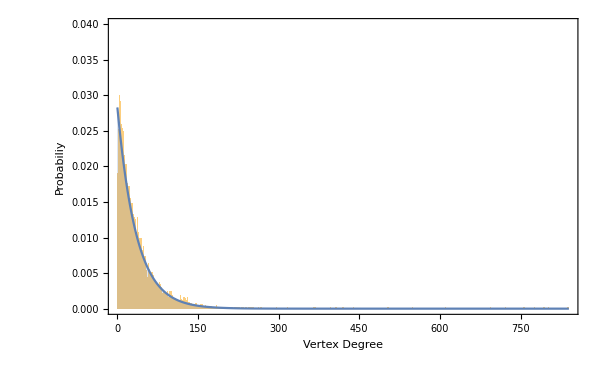

```mathematica
Show[Histogram[VertexDegree[ClassFBall],{0,maxDegree,1},"Probability",PlotRange->{{0,maxDegree},{0,0.04}},FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True],DiscretePlot[Evaluate@PDF[ExponentialDistribution[1/avgDegree],k],{k,0,maxDegree,1}, PlotRange->{{0,maxDegree},{0,0.04}},FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True]]
```

Let’s take a closer look

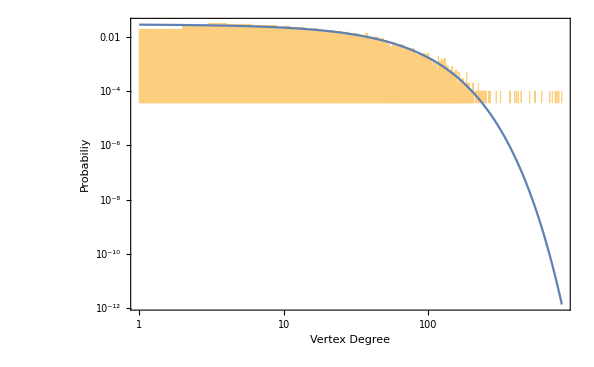

```mathematica
Show[Histogram[VertexDegree[ClassFBall],{0,maxDegree,1},"Probability",ScalingFunctions->{"Log", "Log"},FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True],ListLogLogPlot[Table[Evaluate@PDF[ExponentialDistribution[1/avgDegree],k],{k,0,maxDegree,1}],Joined->True,FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True]]
```

## Power Laws and Scale-Free Networks

Let’s consider the AS graph

```mathematica
ExampleData[{"NetworkGraph","Internet"},"LongDescription"]
```

A symmetrized snapshot of the structure of the Internet at the level of autonomous systems, reconstructed from BGP tables posted by the University of Oregon Route Views Project.

```mathematica
ASgraph = ExampleData[{"NetworkGraph","Internet"}];
```

Size, Max Degree, Average Degree, Min Degree

```mathematica
sizeAS = VertexCount[ASgraph];
maxAS =Max[VertexDegree[ASgraph]];
avgAS =Mean[VertexDegree[ASgraph]]//N;
minAS =Min[VertexDegree[ASgraph]];
Style[TextGrid[{{"","Size", "Max Degree","Average Degree", "Min Degree"},{"AS Graph",sizeAS,maxAS, avgAS, minAS}},Frame->All],20]
```

| Size | Max Degree | Average Degree | Min Degree
AS Graph | 22963 | 2390 | 4.21861 | 1

Wow! one BGP router is connected to 10% of the network

Regular Histogram

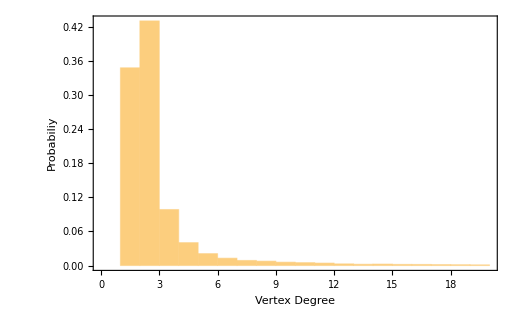

```mathematica
Histogram[VertexDegree[ASgraph],{0,20,1},"Probability",PlotRange->{{0,20},Automatic},FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True]
```

Wow! Almost 80% are degree 1 or 2

```mathematica
Total[Sort[Tally[VertexDegree[ASgraph]]][[{1,2},2]]]/VertexCount[ASgraph]//N
```

0.763837

How does is looks on a log-log scale?

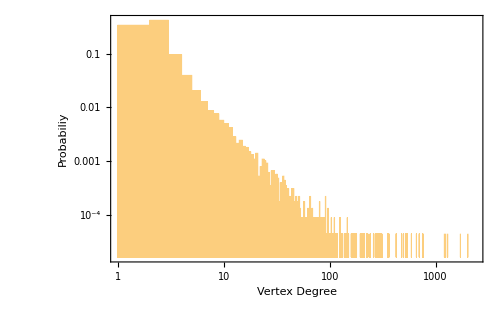

```mathematica
Histogram[VertexDegree[ASgraph],{0,maxAS,1},"Probability",ScalingFunctions->{"Log", "Log"},FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True]
```

“cleaning” the low degree nodes

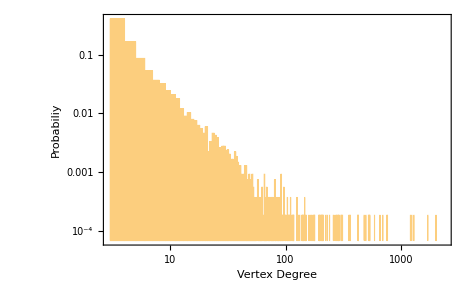

```mathematica
Histogram[VertexDegree[ASgraph],{3,maxAS,1},"Probability",ScalingFunctions->{"Log", "Log"},FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True]
```

Can you “see” the straight line?

Who are the “hubs” (superstars) of the network?

Let’s check again the Exponential Distribution

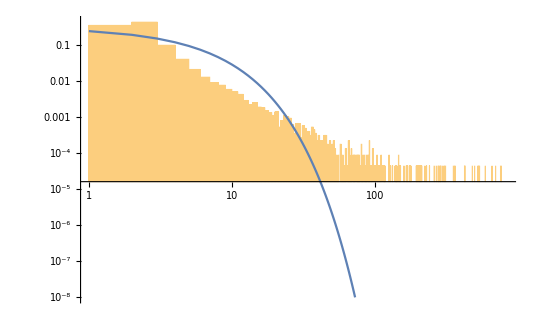

```mathematica
Show[Histogram[VertexDegree[ASgraph],{0,maxDegree,1},"Probability",ScalingFunctions->{"Log", "Log"}],ListLogLogPlot[Table[Evaluate@PDF[ExponentialDistribution[1/avgAS],k],{k,0,maxAS/5,1}],Joined->True,PlotRange->{Automatic,{1,10^-8}}]]
```

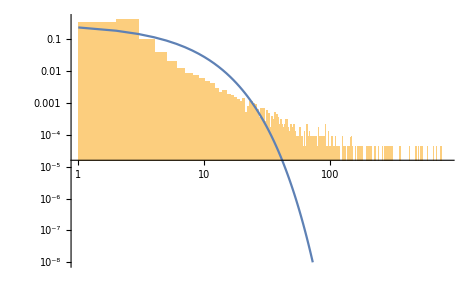

## Power Law Distribution

p_k is Pr(deg = k)

The probability of a random node to be of degree k

p_k ≈ C k^-β

The logarithm of the degree distribution p_k  is a linear function of the logarithm of the degree k

so

ln p_k=-βln k + c

And taking the exponent on both sides

p_k=C k^-β  where C = e^c

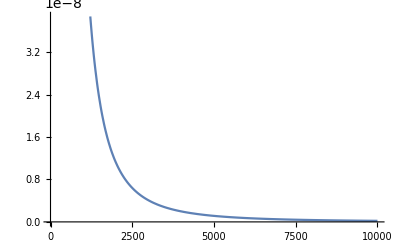

```mathematica
Plot[2 k^-2.5,{k,1,10000}]
```

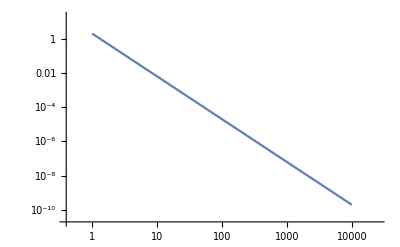

```mathematica
LogLogPlot[2 k^-2.5,{k,1,10000}]
```

β  is the exponent of the power law

β is the slop in the log-log plot

Typically in the range 2 ≤ β ≤ 3

Usually a power law in the tail of the distribution (large degrees)

Networks with power law degree distributions are called “scale free” network

Why “scale free”?

(Pr(bx))/(Pr(x))=f(b)     ∀b,x

In our case

(C(bx)^-β)/(C(x)^-β)=b^-β     ∀b,x

## Power Law in real world

In many places....

Sort and plot (log-log scale)

```mathematica
LargeCities = CityData[{Large,"UnitedStates"}];
Pop =CityData[#,"Population"]&/@ LargeCities;
```

```mathematica
Length[LargeCities]
```

306

```mathematica
Cities = Table[Tooltip[Pop[[i]], LargeCities[[i]]],{i,1,Length[LargeCities]}];
```

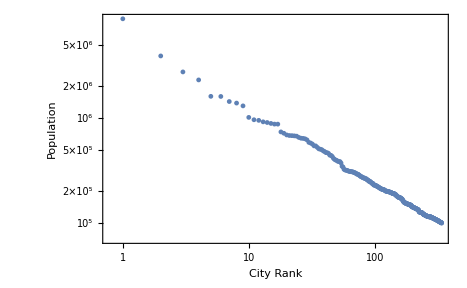

```mathematica
ListLogLogPlot[Cities,PlotRange->All,Frame->True,FrameLabel->{"City Rank", "Population"}]
```

```mathematica
{Pop[[1]],LargeCities[[1]]}
```

{8336697,New York City}

```mathematica
{Pop[[2]],LargeCities[[2]]}
```

{3857799,Los Angeles}

```mathematica
{Pop[[3]],LargeCities[[3]]}
```

{2714856,Chicago}

AS graph

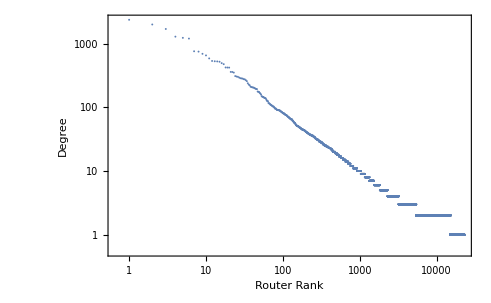

```mathematica
ListLogLogPlot[Sort[VertexDegree[ASgraph],Greater],PlotRange->All,Frame->True,FrameLabel->{"Router Rank", "Degree"}]
```

Why if sorting a power law the distribution is a power law?

If after sorting we have the sizes C(1/1, 1/2^β,1/3^β, 1/4^β,...)

There are i elements larger than C/i^β

Pr(k ≥ C/i^β) = i/N

Pr(k > x) = C’ x^(-1/β)

## Detecting Power Laws

Regular Bins

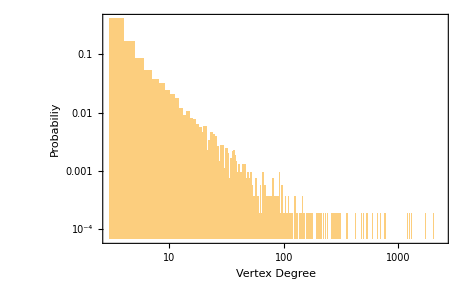

```mathematica
Histogram[VertexDegree[ASgraph],{3,maxAS,1},"Probability",ScalingFunctions->{"Log", "Log"},FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True]
```

Noise

Scatter Plot

```mathematica
DegreeFreq[g_]:=Map[{#⟦1⟧,#⟦2⟧/VertexCount[g]}&,Tally[VertexDegree[g]]];
```

```mathematica
CumDigDist[g_,min_,max_]:=Module[{df,cm,minpos,maxpos},
df =Sort[DegreeFreq[g],#1[[1]]<#2[[1]]&];
minpos=First@First@Position[df[[All,1]],min];
maxpos=First@First@Position[df[[All,1]],max];cm =Reverse[Accumulate[Reverse[df[[All,2]]]]];Transpose[{df[[minpos;;maxpos,1]],cm[[minpos;;maxpos]]}]]
```

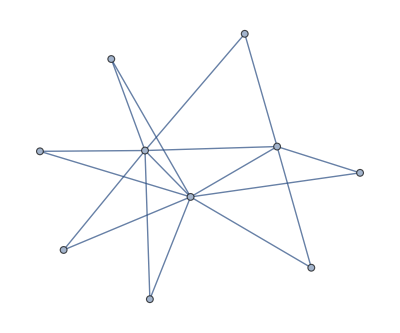

Degree | DegreeCount | DegreeFrequency | Cumulative
2 | 7 | 7/10 | 1
5 | 1 | 1/10 | 3/10
7 | 1 | 1/10 | 1/5
8 | 1 | 1/10 | 1/10

```mathematica
rg=RandomGraph[BarabasiAlbertGraphDistribution[10,2]]
TableForm[Transpose[{CumDigDist[rg,Min[VertexDegree[rg]],Max[VertexDegree[rg]]][[All,1]],Sort[Tally[VertexDegree[rg]],#1[[1]]<#2[[1]]&][[All,2]],Sort[DegreeFreq[rg],#1[[1]]<#2[[1]]&][[All,2]],CumDigDist[rg,Min[VertexDegree[rg]],Max[VertexDegree[rg]]][[All,2]]}],TableHeadings-> {None,{"Degree", "DegreeCount","DegreeFrequency","Cumulative"}}]
```

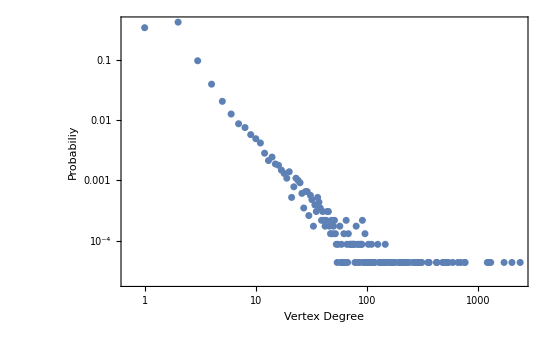

```mathematica
ListLogLogPlot[DegreeFreq[ASgraph],FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True,PlotRange->All]
```

Logarithmic Binning (reduce noise)

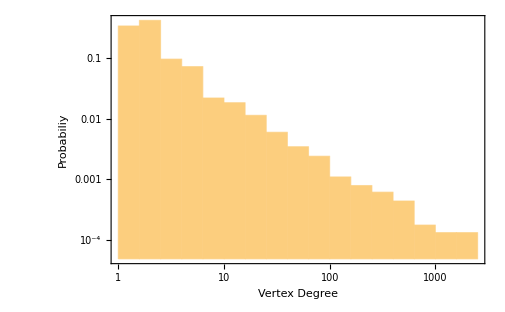

```mathematica
Histogram[VertexDegree[ASgraph],"Log",{"Log","Probability"},FrameLabel-> {"Vertex Degree", "Probabiliy"}, Frame->True]
```

## Cumulative Distribution

(P̂)_k= ∑_(k'=k)^∞ p_k

Fraction of vertices that have degree k or larger

Notice that for power law distribution

p_k=C k^-α

(P̂)_k= ∑_(k'=k)^∞ C k^-α  ≃C∫_(k'=k)^∞ k'^-α ⅆk' = C/(α-1)k^(-(α-1))

Also a power law!

Easy to generate

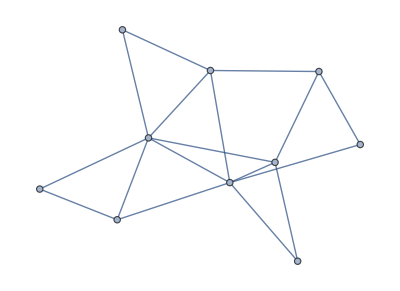

Degree | DegreeCount | DegreeFrequency | Cumulative
2 | 4 | 2/5 | 1
3 | 2 | 1/5 | 3/5
4 | 2 | 1/5 | 2/5
6 | 2 | 1/5 | 1/5

```mathematica
rg=RandomGraph[BarabasiAlbertGraphDistribution[10,2]]
TableForm[Transpose[{CumDigDist[rg,Min[VertexDegree[rg]],Max[VertexDegree[rg]]][[All,1]],Sort[Tally[VertexDegree[rg]],#1[[1]]<#2[[1]]&][[All,2]],Sort[DegreeFreq[rg],#1[[1]]<#2[[1]]&][[All,2]],CumDigDist[rg,Min[VertexDegree[rg]],Max[VertexDegree[rg]]][[All,2]]}],TableHeadings-> {None,{"Degree", "DegreeCount","DegreeFrequency","Cumulative"}}]
```

The Cumulative degree distribution of the AS graph

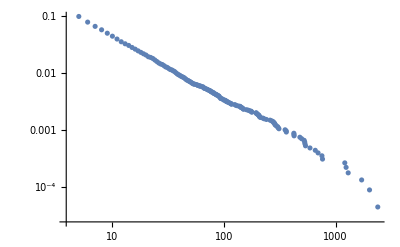

```mathematica
ListLogLogPlot[CumDigDist[ASgraph,5,maxAS]]
```

Can we find the slop? The exponent

```mathematica
ASfit =Fit[Log[CumDigDist[ASgraph,5,maxAS]],{1,x},x]
```

-0.576474-1.10031 x

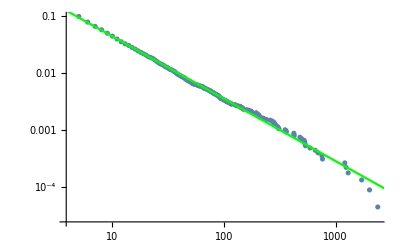

```mathematica
Show[ListLogLogPlot[CumDigDist[ASgraph,5,maxAS]],Plot[ASfit,{x,1,1000},PlotStyle->Green]]
```

So the slop (of the degree distribution) is about  -2.1 and α ≈2.1.

```mathematica
-ASfit[[2]][[1]]+1
```

2.10031

```mathematica
socialNet=ExampleData[{"NetworkGraph","CondensedMatterCollaborations"}];
```

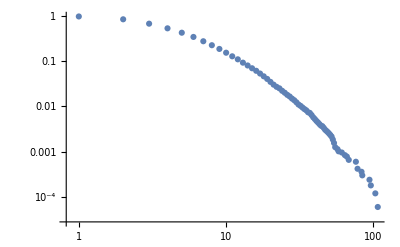

```mathematica
ListLogLogPlot[CumDigDist[socialNet,Min[VertexDegree[socialNet]],Max[VertexDegree[socialNet]]]]
```

```mathematica
Powerfit =Fit[Log[CumDigDist[socialNet,5,58]],{1,x},x]
```

3.92705-2.50348 x

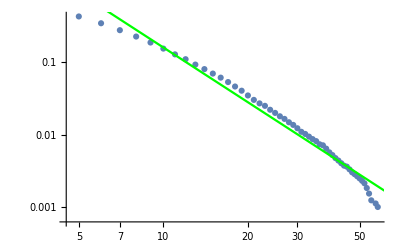

```mathematica
Show[ListLogLogPlot[CumDigDist[socialNet,5,58]],Plot[Powerfit,{x,1,58},PlotStyle->Green]]
```

## Properties of Power Laws Distributions

Normalization

p_k=C k^-β

1=C∫_(k'=k_min)^∞ k'^-β ⅆk'= (([C/(1-β)k^(-(β-1))]^∞)_k_min)_(.08)

C=(β-1)(k_min^(β-1))_(.08)

p_k=(β-1)/k_min (k/k_min)^-β

First Moment

<k>=C∫_k_min^∞ k·k^-βⅆk=C∫_k_min^∞ k^(-β+1)ⅆk =(([C/(2-β)k^(-β+2)]^∞)_k_min)_(.08)

If β > 2

<k>=C/(β-2)k_min^(-β+2)=(β-1)/(β-2)k_min

Second Moment

<k>=C∫_k_min^∞ k^2·k^-βⅆk=C∫_k_min^∞ k^(-β+2)ⅆk =(([C/(3-β)k^(-β+3)]^∞)_k_min)_(.08)

α must be s.t. β > 3 for a meaningful variance....

## Preferential Attachment Model - Generating Power law networks

Network Formation

Nodes arrive one by one (people, pages, routers)

Preferential Attachment (PA) - “rich get richer”

high degree nodes attracts new nodes

New nodes connects to existing nodes with probability

Π(i)=k_i/(∑_j k_j)= k_i/(2m)

If node i has twice the degree of node j than is has twice the probability to be chosen!

Generates a scale free network (with β = 3)

Show Example (netlogo)

(aka) BarabasiAlbertGraphDistribution

## Let’s generate the Internet....

```mathematica
PaAS= RandomGraph[BarabasiAlbertGraphDistribution[VertexCount[ASgraph],Round[EdgeCount[ASgraph]/VertexCount[ASgraph]]]];
```

```mathematica
VertexCount[PaAS]
```

22963

```mathematica
Mean[VertexDegree[PaAS]]//N
```

3.99974

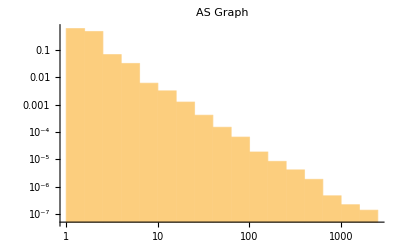
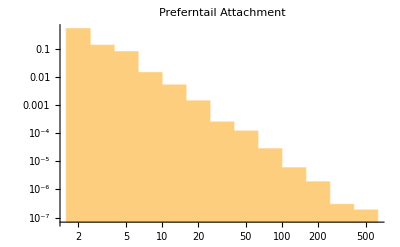

```mathematica
{Histogram[VertexDegree[ASgraph],{"Log",15},{"Log","PDF"},PlotLabel->"AS Graph"],Histogram[VertexDegree[PaAS],{"Log",15},{"Log","PDF"},PlotLabel->"Preferntail Attachment"]}
```

```mathematica
maxPaAS =Max[VertexDegree[PaAS]];
```

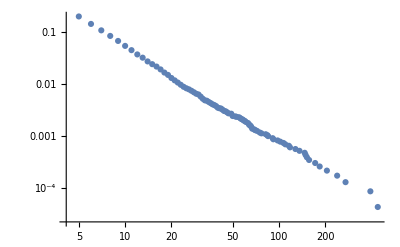

```mathematica
ListLogLogPlot[CumDigDist[PaAS,5,maxPaAS]]
```

```mathematica
PAfit =Fit[Log[CumDigDist[PaAS,5,maxPaAS]],{1,x},x]
```

1.09582-1.79692 x

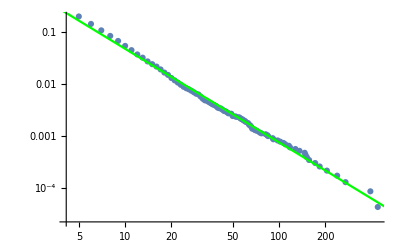

```mathematica
Show[ListLogLogPlot[CumDigDist[PaAS,5,maxPaAS]],Plot[PAfit,{x,1,1000},PlotStyle->Green]]
```

α is:

```mathematica
-PAfit[[2]][[1]]+1
```

2.91542

Close, but not the same....

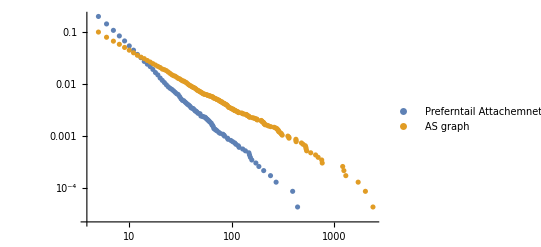

```mathematica
ListLogLogPlot[{CumDigDist[PaAS,5,maxPaAS],CumDigDist[ASgraph,5,maxAS]},PlotLegends->{"Preferntail Attachemnet","AS graph"}]
```

One last thing....

```mathematica
N[GlobalClusteringCoefficient[PaAS]]
```

0.000741043

```mathematica
N[GlobalClusteringCoefficient[ASgraph]]
```

0.0111464

## Class Homework

1. Find a network with power law degree distribution. Plot the degree distribution and try to find power exponent β.

```mathematica
2. Generate the symmetry point graph for PA with sevral sizes (on what fraction it is happends? what is the "core" fraction)
```

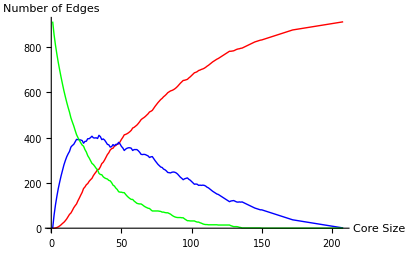

3. Add Preferential Attachment to the models you check “Network of Throne” with.